Various rough calculations and plots for ps3, p3.

```mathematica
Integrate[ Sin[t]^3, {t, 0, Pi}]
Integrate[ Sin[t]^5, {t, 0, Pi}]
Integrate[ Sin[2t], {t, 0, Pi/2}]
```

4/3

16/15

1

```mathematica
(2 Pi/3) (16/15) // N // Sqrt
```

1.49466

```mathematica
af[a_,p_] = 3 - 2 Cos[ 2 Pi a Cos[p] ] - 2 Cos[ 2 Pi a Sin[p]] + 2 Cos[ 2 Pi a (Cos[p] - Sin[p])] ;
pp = Plot3D[ af[a,p], {a, 0, 1.5}, {p, 0, 2 Pi}, AxesLabel -> {α, ϕ}]
```

-Graphics3D-

```mathematica
peeters`exportForLatex["arrayFactorXYFig4", pp]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYFig4.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYFig4pn.png}

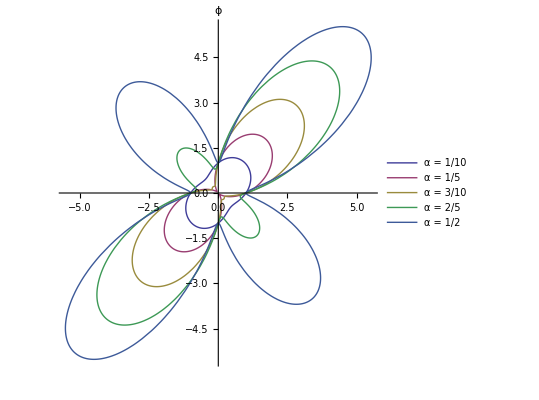

```mathematica
(*aa = {0.5} ;
aa = {0.1, 0.25, 0.5, 0.75, 1} ;*)
aa = Table[i/10, {i, 5}] ;
xx = PolarPlot[af[#, p] &/@ aa // Evaluate, {p, 0, 2 Pi}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"α = ", #}]&/@aa, {Right,Bottom}]]
```

```mathematica
peeters`exportForLatex["arrayFactorXYFig5", xx]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYFig5.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/arrayFactorXYFig5pn.png}